```mathematica
OGHCoefs[P0_,V0_,P1_, V1_] := {
(6(P1-P0).V0 - 3 (P1-P0).V1 (V0.V1))/(4-(V0.V1)^2),
(3(P1-P0).V0 (V0.V1)- 6 (P1-P0).V1)/((V0.V1)^2-4)
}
```

```mathematica
Arc2D[p1_, t1_,p2_, t2_] := Module[{Δp, Δθ, n1,offset, controlpoints, a0, a1},
(*Δp=p2-p1;

Δθ = ArcCos[Clip[t1.t2, {-1, 1}]];
offset=(1/3 +Δθ^2/18) Norm[Δp] ;
controlpoints={p1,p1+offset t1,p2-offset t2,p2};

Arrow[Table[
{-(-1+t)^3,3 (-1+t)^2 t,-3 (-1+t) t^2,t^3}.controlpoints
,
{t, 0, 1, 0.01}
]];*)


{a0, a1} = OGHCoefs[p1,t1, p2,t2];
Line[Table[
 {(2t+1)(t-1)^2, a0(1-t)^2 t, (3-2t)t^2, (t-1)t^2 a1}.{p1, t1, p2, t2}
,
{t, 0, 1, 0.01}
]]
]
```

```mathematica
paths = BinaryReadList["C:\\Users\\sam\\Documents\\Github\\RLUtilities\\rlutilities\\assets\\paths_planar.bin" , "UnsignedInteger32"];
times = BinaryReadList["C:\\Users\\sam\\Documents\\Github\\RLUtilities\\rlutilities\\assets\\times_planar.bin" , "Real32"];
{scale, gx, ntheta, nv, tmp} =Flatten[Import["C:\\Users\\sam\\Documents\\Github\\RLUtilities\\rlutilities\\assets\\parameters.txt", "Table"]];



c = Table[Cos[(2.0π (i-1))/ntheta], {i, 1, ntheta}];
s = Table[Sin[(2.0π (i-1))/ntheta], {i, 1, ntheta}];

tangents = Table[{c[[i]], s[[i]]}, {i, 1, ntheta}];
strides = {nv * ntheta * (2 * gx + 1), nv* ntheta, nv, 1};


toId[t_] := Module[{},
(t[[1]] + gx) * strides[[1]] +
(t[[2]] + gx) * strides[[2]] +
t[[3]] * strides[[3]]+
t[[4]] * strides[[4]]
]

fromId[i_] := Module[{id = i, x, y, θ, v},
x=Quotient[id,strides[[1]]];id=Mod[id,strides[[1]]];
y=Quotient[id,strides[[2]]];id=Mod[id,strides[[2]]];
θ=Quotient[id,strides[[3]]];id=Mod[id,strides[[3]]];
v=Quotient[id,strides[[4]]];
{x-gx, y-gx, θ, v}
]
```

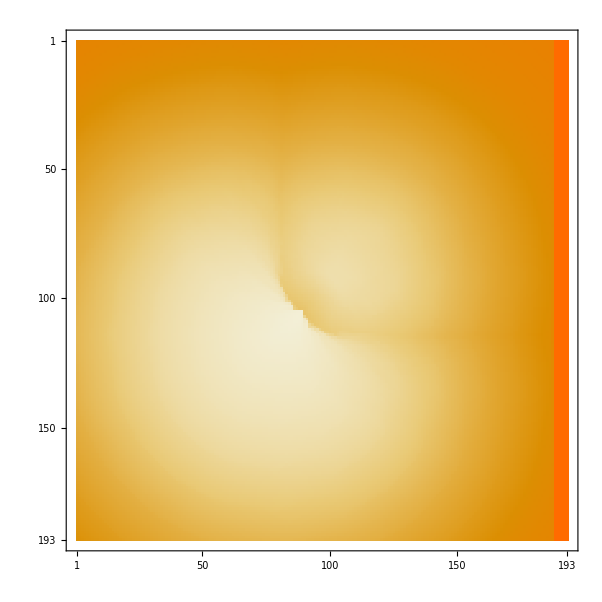

```mathematica
v =12;
θ = 12;
tmp = Table[times[[toId[{x, y, θ, v}]+1]], {x, -gx, gx}, {y, -gx, gx}];
MatrixPlot[tmp]
```

```mathematica
Follow[destination_] := Module[{id = toId[destination]},
list = {destination};
While[fromId[id][[1;;3]]≠{0, 0, 0},
id = paths[[id+1]];
AppendTo[list, fromId[id]];
];
list = Reverse[list];
Table[Arc2D[
list[[i, 1;;2]], 
tangents[[list[[i, 3]]+1]],
list[[i+1, 1;;2]], 
tangents[[list[[i+1, 3]]+1]]
], {i, 1, Length[list]-1}]
]
```

```mathematica
Manipulate[
Graphics[{
Arrowheads[0.02],
Follow[{Round[p[[1]]], Round[p[[2]]],θ,v}]
}, 
PlotRange->{{-1, 1}, {-1, 1}}*gx]
,
{{p,{5, 0}}, Locator},
{θ, 0, 15, 1},
{v, 3, 22, 1}
]
```

```mathematica
controlpoints = {#[[1;;2]], tangents[[#[[3]]+1]]} & /@ list;
```

```mathematica
Do[
prev = controlpoints[[i-1]];
mine = controlpoints[[i]];
next = controlpoints[[i+1]];

ϕ1=ArcSin[Det[{mine[[2]], Normalize[(mine-prev)[[1]]]}]];
ϕ2=ArcSin[Det[{mine[[2]], Normalize[(next-mine)[[1]]]}]];

Print[{ϕ1, ϕ2}];

ϕ = Clip[If[Abs[ϕ1]<Abs[ϕ2], ϕ1, ϕ2], π/ntheta{-1, 1}];

If[ϕ1 ϕ2>0(*&&Min[Abs[ϕ1], Abs[ϕ2]] < π/ntheta*),
controlpoints[[i,2]] = RotationMatrix[ϕ].controlpoints[[i,2]];
]
,
{i,2,Length[controlpoints]-1}
]
```

{-0.132097,-0.195304}

{0.197396,0.197396}

{-0.195304,0.392699}

{-0.392699,0.282042}

{-0.503356,0.590095}

```mathematica
π/(2.0ntheta)
```

0.0981748

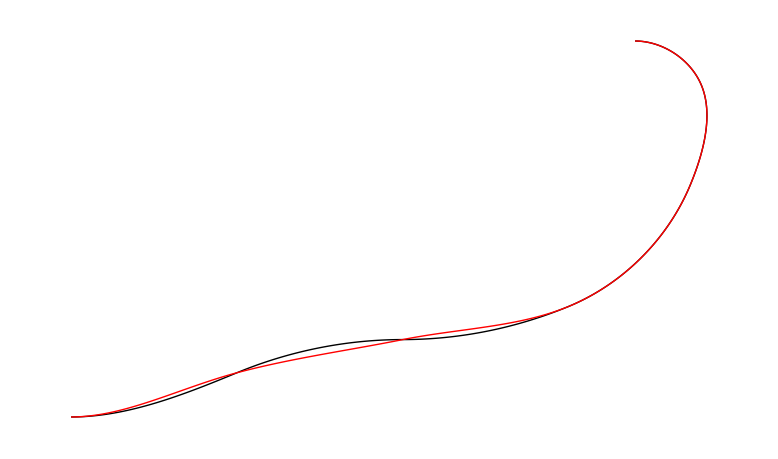

```mathematica
Graphics[{Table[Arc2D[
list[[i, 1;;2]], 
tangents[[list[[i, 3]]+1]],
list[[i+1, 1;;2]], 
tangents[[list[[i+1, 3]]+1]]
], {i, 1, Length[list]-1}],
Red,
Table[Arc2D[
controlpoints[[i, 1]], 
controlpoints[[i, 2]],
controlpoints[[i+1, 1]],
controlpoints[[i+1, 2]]
], {i, 1, Length[controlpoints]-1}]
}]
```